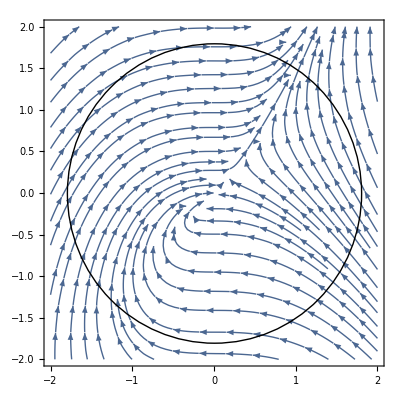

```mathematica
xdot = y-x;
ydot = x^2;
streamPlot= StreamPlot[{xdot, ydot}, {x,-2, 2},{y,-2,2}];
circle = Graphics[Circle[{0,0}, 1.8]];
Show[streamPlot,circle]
```

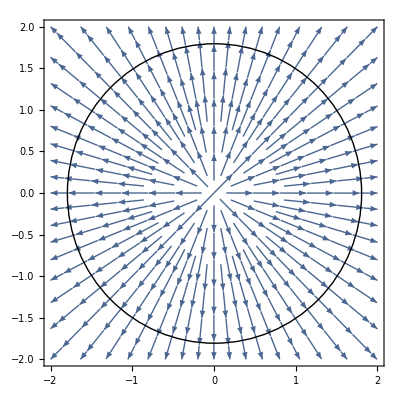

```mathematica
a = 1;
xdot = a*x;
ydot = a*y;
streamPlot= StreamPlot[{xdot, ydot}, {x,-2, 2},{y,-2,2}];
circle = Graphics[Circle[{0,0}, 1.8]];
Show[streamPlot,circle]
```

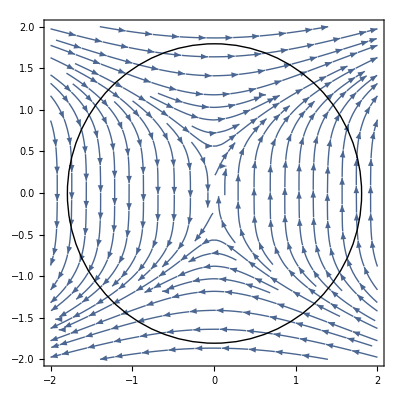

```mathematica
xdot = y^3;
ydot = x;
streamPlot= StreamPlot[{xdot, ydot}, {x,-2, 2},{y,-2,2}];
circle = Graphics[Circle[{0,0}, 1.8]];
Show[streamPlot,circle]
```

```mathematica
xdot = (x^2+y^2)^(Abs[n]/2) *Cos[n*ArcTan[y/x]];
ydot = (x^2+y^2)^(Abs[n]/2) *Sin[n*ArcTan[y/x]];
Graphics[Circle[{0,0}, 1.8]];
Manipulate[Show[StreamPlot[{xdot, ydot}/.{n->n0}, {x,-2, 2},{y,-2,2}], circle], {n0,1,20,1}]
```